```mathematica
maxorientations2[graph_]:=Monitor[Block[{j=0,blist={},bestlist={},bestlen=1,uelist=Map[{#[[1]],#[[2]]}&,EdgeList[graph]],len=Length[EdgeList[graph]]},
For[j=0,j<2^len,j++,blist=PadLeft[IntegerDigits[j,2],len];
Block[{thislen=Length[FindCycle[Graph[Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,len}]],∞,All]]},If[thislen≥bestlen,AppendTo[bestlist,{thislen,j}];bestlen=thislen]]];
Block[{allmax=Max[Map[First,bestlist]]},
Map[Graph[Table[Piecewise[{{Map[{#[[1]],#[[2]]}&,EdgeList[graph]][[i]][[1]]->Map[{#[[1]],#[[2]]}&,EdgeList[graph]][[i]][[2]], PadLeft[IntegerDigits[#,2],len][[i]]==0}, {Map[{#[[1]],#[[2]]}&,EdgeList[graph]][[i]][[2]]->Map[{#[[1]],#[[2]]}&,EdgeList[graph]][[i]][[1]], PadLeft[IntegerDigits[#,2],len][[i]]==1}}],{i,1,len}]]&,Map[Last,Select[bestlist,First[#]==allmax&]]]
]],{j,i}]
```

```mathematica
nthor[graph_,n_]:=
Block[{uelist=Map[{#[[1]],#[[2]]}&,EdgeList[graph]],len=Length[EdgeList[graph]]},
Block[{blist=PadLeft[IntegerDigits[n,2],len]},
Graph[Table[Piecewise[{{uelist[[i]][[1]]->uelist[[i]][[2]], blist[[i]]==0}, {uelist[[i]][[2]]->uelist[[i]][[1]], blist[[i]]==1}}],{i,1,len}]]]]
```

```mathematica
numcy[g_]:=Length[FindCycle[g,∞,All]]
```

```mathematica
Table[numcy[nthor[CycleGraph[3],i]],{i,0,2^3-1}]//Column
```

0
0
1
0
0
1
0
0

```mathematica
Table[MatrixForm[MatrixPower[AdjacencyMatrix[nthor[CycleGraph[3],2]],j]],{j,1,4}]
```

{(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0),(0 | 0 | 1
1 | 0 | 0
0 | 1 | 0),(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0)}

```mathematica
EdgeCount[CompleteGraph[5]]
```

10

```mathematica
ArrayPlot[AdjacencyMatrix[CompleteGraph[4]],ImageSize->Tiny]
```

-Graphics-

```mathematica
MatrixForm[Mod[MatrixPower[AdjacencyMatrix[CompleteGraph[4]],2],2]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
"0 cycles -> some power is zero matrix";
"1 cycles -> det 0 and no power zero matrix & cyclic w/ no identity";
"all cycles -> det -1 and divergent";
```

```mathematica
Sort[DeleteDuplicates[Table[Block[{gr=nthor[CompleteGraph[4],i]},{numcy[gr],Det[AdjacencyMatrix[gr]]}],{i,0,2^EdgeCount[CompleteGraph[4]]-1}]]]
```

{{0,0},{1,0},{3,-1}}

```mathematica
Sort[DeleteDuplicates[Table[Block[{gr=nthor[CompleteGraph[5],i]},{numcy[gr],Det[AdjacencyMatrix[gr]]}],{i,0,2^EdgeCount[CompleteGraph[5]]-1}]]]
```

{{0,0},{1,0},{3,0},{6,1},{7,1},{9,1},{9,2},{10,3},{12,2}}

```mathematica
Sort[DeleteDuplicates[Table[Block[{gr=nthor[CompleteGraph[6],i]},{numcy[gr],Det[AdjacencyMatrix[gr]]}],{i,0,2^EdgeCount[CompleteGraph[6]]-1}]]]
```

{{0,0},{1,0},{2,1},{3,0},{6,0},{7,0},{9,0},{10,0},{12,-1},{12,0},{15,-1},{16,-1},{20,-2},{20,-1},{21,-2},{21,-1},{22,-2},{23,-2},{26,-3},{26,-2},{27,-2},{28,-3},{31,-1},{32,-2},{34,-4}}

```mathematica
EdgeCount[CompleteGraph[6]]
```

15

```mathematica
EdgeCount[WheelGraph[8]]
```

14

```mathematica
Monitor[Sort[DeleteDuplicates[Table[Block[{gr=nthor[WheelGraph[4],i]},{numcy[gr],Det[AdjacencyMatrix[gr]]}],{i,0,2^EdgeCount[WheelGraph[4]]-1}]]],i]
```

{{0,0},{1,0},{3,-1}}

```mathematica
Monitor[Sort[DeleteDuplicates[Table[Block[{gr=nthor[WheelGraph[5],i]},{numcy[gr],Det[AdjacencyMatrix[gr]]}],{i,0,2^EdgeCount[WheelGraph[5]]-1}]]],i]
```

{{0,0},{1,0},{2,0},{4,0},{4,1},{5,1},{5,2}}

```mathematica
Monitor[Sort[DeleteDuplicates[Table[Block[{gr=nthor[WheelGraph[6],i]},{numcy[gr],Det[AdjacencyMatrix[gr]]}],{i,0,2^EdgeCount[WheelGraph[6]]-1}]]],i]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,-1},{5,0},{6,-1},{6,0},{7,-2},{7,-1}}

```mathematica
Monitor[Sort[DeleteDuplicates[Table[Block[{gr=nthor[WheelGraph[7],i]},{numcy[gr],Det[AdjacencyMatrix[gr]]}],{i,0,2^EdgeCount[WheelGraph[7]]-1}]]],i]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{6,1},{7,0},{7,1},{8,0},{8,1},{9,1},{9,2},{10,1},{10,2},{10,3}}

```mathematica
Monitor[Sort[DeleteDuplicates[Table[Block[{gr=nthor[WheelGraph[8],i]},{numcy[gr],Det[AdjacencyMatrix[gr]]}],{i,0,2^EdgeCount[WheelGraph[8]]-1}]]],i]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,-1},{7,0},{8,-1},{8,0},{9,-1},{9,0},{10,-1},{10,0},{11,-2},{11,-1},{11,0},{12,-1},{13,-3},{13,-2},{13,-1}}

```mathematica
Monitor[Sort[DeleteDuplicates[Table[Block[{gr=nthor[WheelGraph[9],i]},{numcy[gr],Det[AdjacencyMatrix[gr]]}],{i,0,2^EdgeCount[WheelGraph[9]]-1}]]],i]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{8,1},{9,0},{9,1},{10,0},{10,1},{11,0},{11,1},{12,0},{12,1},{13,0},{13,1},{13,2},{14,0},{14,1},{15,1},{16,1},{16,2},{16,3},{17,1},{17,2},{17,3},{17,4}}

```mathematica
fh[h_]:=Monitor[Sort[DeleteDuplicates[Table[Block[{gr=nthor[h,i]},{numcy[gr],Det[AdjacencyMatrix[gr]]}],{i,0,2^EdgeCount[h]-1}]]],i]
```

```mathematica
goodgraph[graph_]:=Block[{vd=And@@Map[#>2&,VertexDegree[graph]]},Piecewise[{{Block[{vc=VertexConnectivity[graph]},Piecewise[{{Block[{ec=EdgeConnectivity[graph]},Piecewise[{{Block[{cyd=Length[FindCycle[graph,∞,3]]},Piecewise[{{True, cyd==3}, {False, cyd≠3}}]], ec>1}, {False, ec≤1}}]], vc>1}, {False, vc≤1}}]], vd}, {False, ¬vd}}]]
gedges[graph_]:=Block[{ged=(Length[EdgeList[graph]]≤15)},Piecewise[{{goodgraph[graph], ged}, {False, ¬ged}}]]
lt17= Select[GraphData[;;20],gedges[GraphData[#]]&];
```

```mathematica
Length[lt17]
```

176

```mathematica
Monitor[Table[{lt17[[k]],fh[GraphData[lt17[[k]]]]},{k,1,176}],k]
```

{{{6,114},{{0,0},{1,0},{2,0},{3,0},{4,0},{5,-1},{5,0},{6,-1},{6,0},{7,-2},{7,-1}}},{{6,130},{{0,0},{1,0},{2,0},{2,1},{3,0},{5,-1},{5,0},{5,1},{6,-1},{6,0},{6,1},{7,-1},{9,-1}}},172,{{Wheel,7},{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{6,1},{7,0},{7,1},{8,0},{8,1},{9,1},{9,2},{10,1},{10,2},{10,3}}},{{Wheel,8},{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,-1},{7,0},{8,-1},{8,0},{9,-1},{9,0},{10,-1},{10,0},{11,-2},{11,-1},{11,0},{12,-1},{13,-3},{13,-2},{13,-1}}}}
 |  |  |  |

```mathematica
ot=Out[8];
```

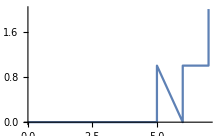
{{6,114},-Graphics-}

```mathematica
abses[l_]:={First[l],ListPlot[Sort[Map[{Abs[#[[1]]],Abs[#[[2]]]}&,Last[l]]],Joined->True]}
abses[{{6,114},{{0,0},{1,0},{2,0},{3,0},{4,0},{5,-1},{5,0},{6,-1},{6,0},{7,-2},{7,-1}}}]
```

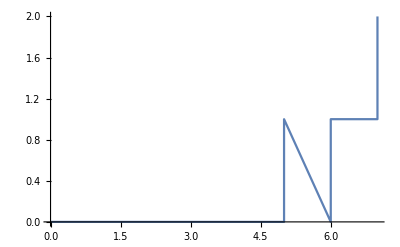
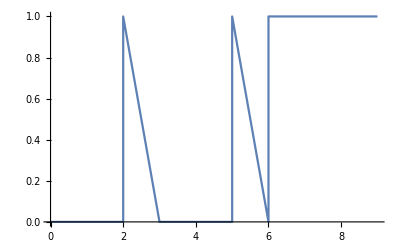
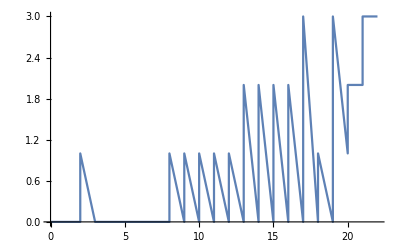
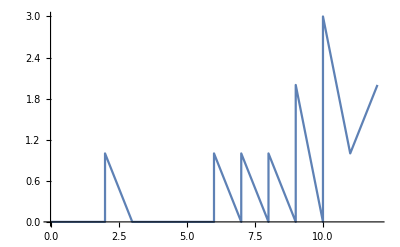
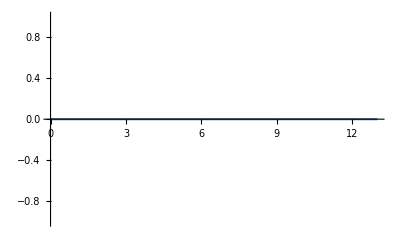
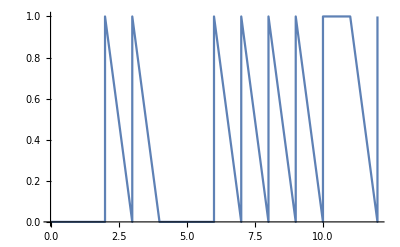
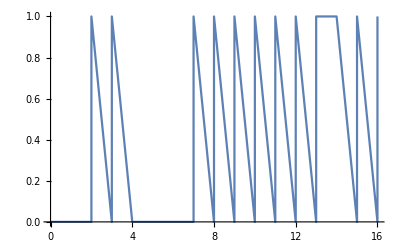
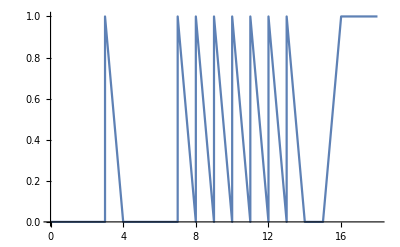
{{6,114},-Graphics-}
{{6,130},-Graphics-}
{{6,148},-Graphics-}
{{6,149},-Graphics-}
{{7,344},-Graphics-}
{{7,550},-Graphics-}
{{7,551},-Graphics-}
{{7,552},-Graphics-}
{{7,553},-Graphics-}
{{7,737},-Graphics-}
{{7,738},-Graphics-}
{{7,740},-Graphics-}
{{7,763},-Graphics-}
{{7,764},-Graphics-}
{{7,765},-Graphics-}
{{7,766},-Graphics-}
{{7,767},-Graphics-}
{{7,768},-Graphics-}
{{7,770},-Graphics-}
{{7,771},-Graphics-}
{{7,772},-Graphics-}
{{7,839},-Graphics-}
{{7,840},-Graphics-}
{{7,841},-Graphics-}
{{7,842},-Graphics-}
{{7,843},-Graphics-}
{{7,844},-Graphics-}
{{7,845},-Graphics-}
{{7,846},-Graphics-}
{{7,888},-Graphics-}
{{7,889},-Graphics-}
{{7,890},-Graphics-}
{{7,892},-Graphics-}
{{7,893},-Graphics-}
{{7,894},-Graphics-}
{{7,895},-Graphics-}
{{7,896},-Graphics-}
{{7,897},-Graphics-}
{{7,899},-Graphics-}
{{7,901},-Graphics-}
{{7,902},-Graphics-}
{{7,905},-Graphics-}
{{7,906},-Graphics-}
{{7,907},-Graphics-}
{{7,910},-Graphics-}
{{7,934},-Graphics-}
{{7,935},-Graphics-}
{{7,949},-Graphics-}
{{7,952},-Graphics-}
{{7,953},-Graphics-}
{{7,954},-Graphics-}
{{7,955},-Graphics-}
{{7,956},-Graphics-}
{{7,963},-Graphics-}
{{7,964},-Graphics-}
{{7,965},-Graphics-}
{{7,967},-Graphics-}
{{7,968},-Graphics-}
{{7,986},-Graphics-}
{{7,987},-Graphics-}
{{7,988},-Graphics-}
{{7,990},-Graphics-}
{{7,991},-Graphics-}
{{7,1002},-Graphics-}
{{7,1003},-Graphics-}
{{7,1004},-Graphics-}
{{7,1008},-Graphics-}
{{7,1009},-Graphics-}
{{7,1013},-Graphics-}
{{7,1017},-Graphics-}
{{7,1018},-Graphics-}
{{7,1019},-Graphics-}
{{7,1020},-Graphics-}
{{7,1025},-Graphics-}
{{7,1026},-Graphics-}
{{Apollonian,2},-Graphics-}
{{BiggestLittlePolygon,6},-Graphics-}
{BislitCube,-Graphics-}
{{BlackBishop,{4,4}},-Graphics-}
{{Circulant,{7,{1,2}}},-Graphics-}
{{Complete,6},-Graphics-}
{{CompleteBipartite,{3,4}},-Graphics-}
{{CompleteBipartite,{3,5}},-Graphics-}
{{CompleteTripartite,{1,3,3}},-Graphics-}
{{Cone,{3,3}},-Graphics-}
{{Cone,{3,4}},-Graphics-}
{{Cubic,{8,2}},-Graphics-}
{{Cubic,{8,3}},-Graphics-}
{{Cubic,{10,2}},-Graphics-}
{{Cubic,{10,3}},-Graphics-}
{{Cubic,{10,4}},-Graphics-}
{{Cubic,{10,5}},-Graphics-}
{{Cubic,{10,6}},-Graphics-}
{{Cubic,{10,7}},-Graphics-}
{{Cubic,{10,8}},-Graphics-}
{{Cubic,{10,9}},-Graphics-}
{{Cubic,{10,10}},-Graphics-}
{{Cubic,{10,11}},-Graphics-}
{{Cubic,{10,12}},-Graphics-}
{{Cubic,{10,13}},-Graphics-}
{{Cubic,{10,14}},-Graphics-}
{{Cubic,{10,16}},-Graphics-}
{{Cubic,{10,18}},-Graphics-}
{CubicalGraph,-Graphics-}
{{Fan,{2,4}},-Graphics-}
{{Fan,{2,5}},-Graphics-}
{{Fan,{3,3}},-Graphics-}
{{Fan,{3,4}},-Graphics-}
{{Fan,{4,3}},-Graphics-}
{{GeneralizedPrism,{3,3}},-Graphics-}
{{HamiltonLaceable,{8,7}},-Graphics-}
{{HamiltonLaceable,{8,8}},-Graphics-}
{{HamiltonLaceable,{8,11}},-Graphics-}
{{Harary,{3,7}},-Graphics-}
{{Harary,{3,9}},-Graphics-}
{{Heptahedral,2},-Graphics-}
{{Heptahedral,4},-Graphics-}
{{Heptahedral,5},-Graphics-}
{{Heptahedral,6},-Graphics-}
{{Heptahedral,7},-Graphics-}
{{Heptahedral,8},-Graphics-}
{{Heptahedral,9},-Graphics-}
{{Heptahedral,10},-Graphics-}
{{Heptahedral,11},-Graphics-}
{{Heptahedral,12},-Graphics-}
{{Heptahedral,13},-Graphics-}
{{Heptahedral,15},-Graphics-}
{{Heptahedral,16},-Graphics-}
{{Heptahedral,18},-Graphics-}
{{Heptahedral,20},-Graphics-}
{{Heptahedral,21},-Graphics-}
{{Heptahedral,22},-Graphics-}
{{Heptahedral,23},-Graphics-}
{{Heptahedral,25},-Graphics-}
{{Heptahedral,26},-Graphics-}
{{Heptahedral,27},-Graphics-}
{{Heptahedral,28},-Graphics-}
{{Heptahedral,29},-Graphics-}
{{Heptahedral,30},-Graphics-}
{{Heptahedral,31},-Graphics-}
{{Heptahedral,34},-Graphics-}
{{Hexahedral,3},-Graphics-}
{{Hexahedral,4},-Graphics-}
{{Hexahedral,5},-Graphics-}
{{JohnsonSkeleton,3},-Graphics-}
{{JohnsonSkeleton,12},-Graphics-}
{{JohnsonSkeleton,13},-Graphics-}
{{JohnsonSkeleton,14},-Graphics-}
{{JohnsonSkeleton,26},-Graphics-}
{{JohnsonSkeleton,49},-Graphics-}
{{JohnsonSkeleton,63},-Graphics-}
{{King,{2,3}},-Graphics-}
{{Matchstick,3},-Graphics-}
{{MoebiusLadder,5},-Graphics-}
{MoserSpindle,-Graphics-}
{OctahedralGraph,-Graphics-}
{PentatopeGraph,-Graphics-}
{PetersenGraph,-Graphics-}
{{Prism,3},-Graphics-}
{{Prism,5},-Graphics-}
{{Quartic,{7,1}},-Graphics-}
{{Queen,{2,3}},-Graphics-}
{{SelfComplementary,{8,5}},-Graphics-}
{{SelfComplementary,{8,6}},-Graphics-}
{{SelfComplementary,{8,10}},-Graphics-}
{SelfDualGraph1,-Graphics-}
{SelfDualGraph2,-Graphics-}
{SelfDualGraph3,-Graphics-}
{TetrahedralGraph,-Graphics-}
{{Turan,{6,5}},-Graphics-}
{UtilityGraph,-Graphics-}
{WagnerGraph,-Graphics-}
{{Wheel,5},-Graphics-}
{{Wheel,6},-Graphics-}
{{Wheel,7},-Graphics-}
{{Wheel,8},-Graphics-}

```mathematica
Column[Map[abses,ot]]
```

```mathematica
Sort[DeleteDuplicates[Table[Block[{gr=nthor[CompleteGraph[5],i]},{numcy[gr],Det[AdjacencyMatrix[gr]]}],{i,0,2^10-1}]]]
```

{{0,0},{1,0},{3,0},{6,1},{7,1},{9,1},{9,2},{10,3},{12,2}}

```mathematica
Select[Table[Block[{gr=nthor[CompleteGraph[4],i]},{numcy[gr],Det[AdjacencyMatrix[gr]],Table[ArrayPlot[Mod[MatrixPower[AdjacencyMatrix[gr],j],2],ImageSize->Tiny],{j,1,15}]}],{i,0,2^6-1}],First[#]==3&]//Column
```

{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{3,-1,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}